```mathematica
提取被掩埋在噪声里的余弦信号
```

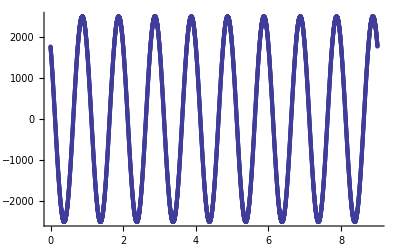

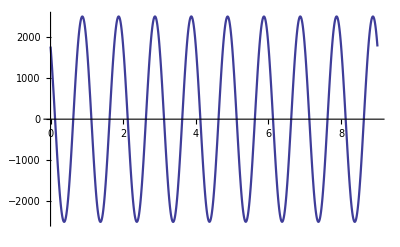

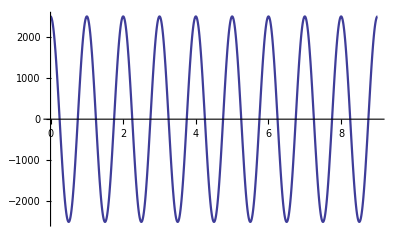

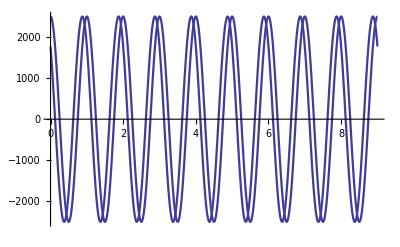

am of corr Y0= 2504.26

am of signal y0= 5.00852

τ=0, C= 1770.98

theoretical ϕ1= 0.785398

calculated ϕ1= 0.785285

{t→0.124995}

ϕ1+ωτ1= 1.57065

```mathematica
T=1.0;n=10^3;δt=T/n;ω=2π/T;
ϕ1=π/4.;x0=1;y0=5;q=10;
s1=Table[x0 Cos[ω δt i],{i,0,n}];
s2=Table[y0 Cos[ω δt  i+ϕ1]
+(Random[]-0.5)/5,{i,0,q n}];
s=ListCorrelate[s1,s2];len=Length[s];
s3=Table[{(i-1) δt,s[[i]]},{i,len}];
ListPlot[s3,AxesStyle->Thickness[0.003],
BaseStyle->{FontSize->13}]
s4=Interpolation[s3];
g1=Plot[s4[t],{t,0,(len-1) δt},
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004],
BaseStyle->{FontSize->13}]
Y=FindMaximum[s4[t],{t,0.8}];
s5[t_]:=Y[[1]]  Cos[ω t];
g2=Plot[s5[t],{t,0,(len-1) δt},
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004],
BaseStyle->{FontSize->13}]
Show[{g1,g2}]
Print["am of corr Y0= ",Y[[1]]]
Print["am of signal y0= ",2δt Y[[1]]/x0]
Print["τ=0, C= ",c=s4[0]]
Print["theoretical ϕ1= ",ϕ1]
Print["calculated ϕ1= ",
ϕ1=ArcCos[c/Y[[1]]]]
τ1=FindRoot[s4[t]==0,{t,0.1}]
Print["ϕ1+ωτ1= ",ϕ1+ω t/.τ1]
Clear[ϕ1,x0,y0,q,s,s1,s2,s3,s4,s5]
```